```mathematica
(*Here, we must first initialize our variables, in order to determine the probability of a transition happening*)
```

```mathematica
f[t_]:=1/10000 Exp[-.5t]*Sin[ω*t]
ω=10;
τ=RandomInteger[{1,20},20];
StochasticY =Table[f[x],{x,20,40}]
StochasticX =Table[x,{x,0,20}]
```

{-3.96476×10^-9,1.28793×10^-9,1.47641×10^-10,-6.24079×10^-10,5.80902×10^-10,-3.61682×10^-10,1.54435×10^-10,-2.41352×10^-11,-3.22475×10^-11,4.17018×10^-11,-3.05828×10^-11,1.57873×10^-11,-4.81825×10^-12,-9.03584×10^-13,2.69225×10^-12,-2.40788×10^-12,1.46043×10^-12,-6.00679×10^-13,7.41373×10^-14,1.45517×10^-13,-1.75388×10^-13}

{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

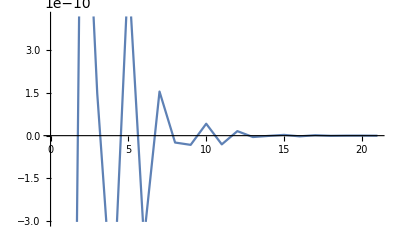

{0,0,0,0,0,0,0,0,-3.96476×10^-9,1.28793×10^-9,1.47641×10^-10,-6.24079×10^-10,5.80902×10^-10,-3.61682×10^-10,1.54435×10^-10,-2.41352×10^-11,-3.22475×10^-11,4.17018×10^-11,-3.05828×10^-11,1.57873×10^-11,-4.81825×10^-12,-9.03584×10^-13,2.69225×10^-12,-2.40788×10^-12,1.46043×10^-12,-6.00679×10^-13,7.41373×10^-14,1.45517×10^-13,-1.75388×10^-13}

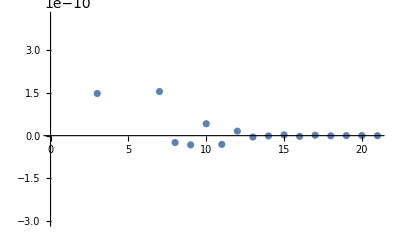

```mathematica
dat1=ListLinePlot[StochasticY]
StochasticY2=Insert[StochasticY,0,{{1},{1},{1},{1},{1},{1},{1},{1}}]
dat2=ListPlot[StochasticY]
```

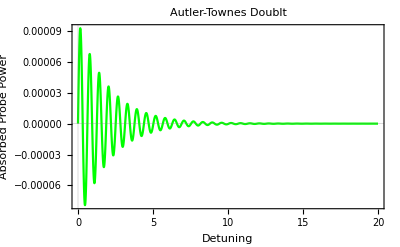

g

```mathematica
dat4=Plot[f[t],{t,0,20},PlotRange->All,Frame->True,FrameLabel->{"Detuning" ,"Absorbed Probe Power"},PlotLabel->"Autler-Townes Doublt",PlotStyle->{Green},PlotTheme->"Scientific",FrameStyle->Directive[GrayLevel[0],Thickness[Medium]]]
Ket[g]
```

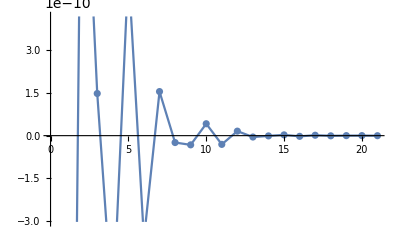

```mathematica
Show[dat1,dat2]
```

21

21

{{0,-0.0000396476},{1,0.0000128793},{2,1.47641×10^-6},{3,-6.24079×10^-6},{4,5.80902×10^-6},{5,-3.61682×10^-6},{6,1.54435×10^-6},{7,-2.41352×10^-7},{8,-3.22475×10^-7},{9,4.17018×10^-7},{10,-3.05828×10^-7},{11,1.57873×10^-7},{12,-4.81825×10^-8},{13,-9.03584×10^-9},{14,2.69225×10^-8},{15,-2.40788×10^-8},{16,1.46043×10^-8},{17,-6.00679×10^-9},{18,7.41373×10^-10},{19,1.45517×10^-9},{20,-1.75388×10^-9}}

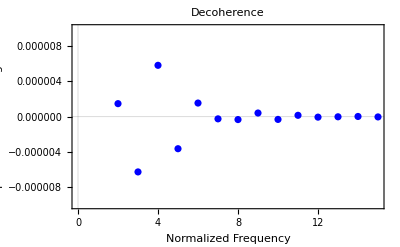

```mathematica
Length[StochasticX]
Length[StochasticY]
findat=Transpose[{StochasticX,10000*StochasticY}]
finplot=ListPlot[findat,PlotRange->{{0,15},{-.00001,.00001}},Frame->True,FrameLabel->{"Normalized Frequency" ,"Population of Atoms in g State"},PlotLabel->"Decoherence",PlotStyle->{Blue},PlotTheme->"Scientific",FrameStyle->Directive[GrayLevel[0],Thickness[Medium]]]
```

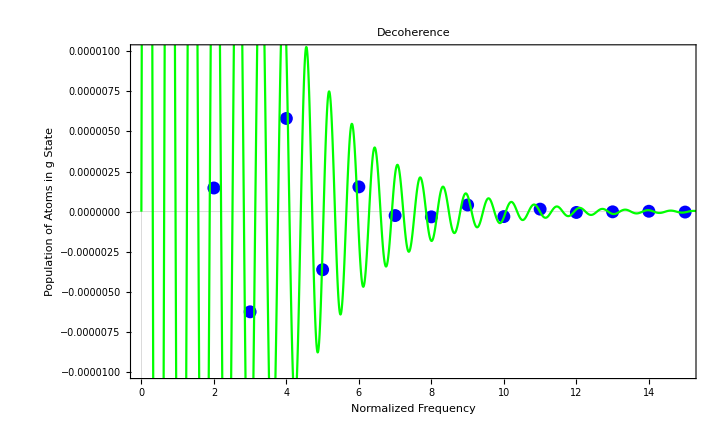

```mathematica
Show[finplot,dat4]
```